```mathematica
bDat=Import["/Users/benxgh1996/Desktop/Hall/results.xlsx",{"Data",1,Range[2,11],{1,2,3}}]
```

{{0.061,0.5,2.5},{0.107,1.1,5.},{0.157,1.6,7.5},{0.205,2.2,10.},{0.251,2.8,12.5},{0.294,3.3,15.},{0.335,3.9,17.5},{0.378,4.5,20.},{0.417,5.,22.5},{0.457,5.6,25.}}

```mathematica
vbDat={#[[3]],#[[1]]}&/@bDat
```

{{2.5,0.061},{5.,0.107},{7.5,0.157},{10.,0.205},{12.5,0.251},{15.,0.294},{17.5,0.335},{20.,0.378},{22.5,0.417},{25.,0.457}}

```mathematica
FindFit[vbDat,a x+b,{a,b},x]
```

{a→0.0176291,b→0.0238}

```mathematica
ibDat={#[[2]],#[[1]]}&/@bDat
```

{{0.5,0.061},{1.1,0.107},{1.6,0.157},{2.2,0.205},{2.8,0.251},{3.3,0.294},{3.9,0.335},{4.5,0.378},{5.,0.417},{5.6,0.457}}

```mathematica
FindFit[ibDat,a x+b,{a,b},x]
```

{a→0.0779231,b→0.0285347}

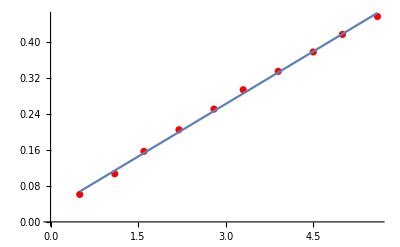

```mathematica
Show[ListPlot[ibDat,PlotStyle->Red],Plot[a x+b/.{a->0.07792306234602994,b->0.028534659844608644},{x,0.5,5.6}]]
```

```mathematica
magI[i_]:=a i+b/.{a->0.07792306234602994,b->0.028534659844608644}
```

```mathematica
{magI[1.3],magI[2.4],magI[3.5]}
```

{0.129835,0.21555,0.301265}

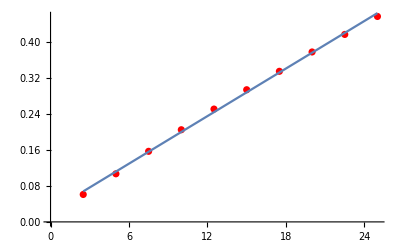

```mathematica
Show[ListPlot[vbDat,PlotStyle->Red],Plot[a x+b/.{a->0.017629090909090907,b->0.023799999999999957},{x,2.5,25.}]]
```

```mathematica
mag[v_]:=a v+b/.{a->0.017629090909090907,b->0.023799999999999957}
```

```mathematica
{mag[6.0],mag[11.0],mag[16.0]}
```

{0.129575,0.21772,0.305865}

```mathematica
0.21772/0.224
```

0.971964

```mathematica
0.129575/0.145
```

0.893621

```mathematica
FindFit[vbDat,a x,a,x]
```

{a→0.0189891}

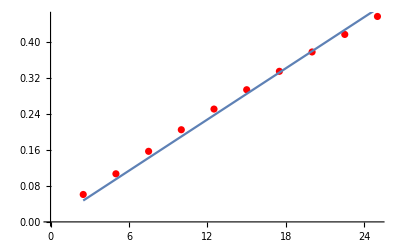

```mathematica
Show[ListPlot[vbDat,PlotStyle->Red],Plot[a x/.{a->0.018989090909090903},{x,2.5,25.}]]
```

```mathematica
mag0[v_]:=a v/.{a->0.018989090909090903};
```

```mathematica
{#,mag0[#]}&/@Range[2.5,25,2.5]//TableForm
```

2.5 | 0.0474727
5. | 0.0949455
7.5 | 0.142418
10. | 0.189891
12.5 | 0.237364
15. | 0.284836
17.5 | 0.332309
20. | 0.379782
22.5 | 0.427255
25. | 0.474727

```mathematica
(*This function plots the V_hall vs. I graphs for a list of data {magnetic field, probe voltage, probe current, hall voltage}
at all magnetic fields.*)
getIvsVhPlot[dat_]:=Module[
{ivDats,a,b},
(*First, we want to obtain a list of list, where each element list contains {I, V_hall} for a fixed magnet voltage.*)
ivDats=getIvsVh[dat,#]&/@MAGVOLTAGES;

(*Then, we wan to find a straight line for each element list.
Remember that ivDats contains I_vs_V_hall lists that correspond to different magnetic fields.
The following statement will generate a list of {a->something, b->something} for each magnetic field.*)
ivFits=FindFit[#,a x+b,{a,b},x]&/@ivDats;
];
(*Obtain a list of {proble current, hall voltage} for a certain magnet voltage. The original data should be under a same temperature.
dat: a transformed list of {magnetic field, probe voltage, probe current, hall voltage};
magV: the magnet voltage that is fixed.*)
getIvsVh[dat_,magV_]:=Module[
{ivDat},
(*First, we want to extract all the data with the desired magnetic field.*)
ivDat=Select[dat,#[[1]]==mag[magV]&];
ivDat={#[[3]],#[[4]]}&/@ivDat;
ivDat
];
```